# Linear system and Applications

## 1. EEL-3120 Introduction to Linear Systems in Engineering

Section: EEL3120 RVC 1201

Year: 2020
Semester: Spring

Group No. 14

Student names: Polina Zhukov, Richard Larancuente
Student PID: 6213707 [Polina PID], 5442696 [Richard PID]

Student’s signatures:

Это версия от 27 декабря 2017 года.

## 2. Abstract

Different techniques can be used to solve a linear system. Often times, large linear systems are encountered in the real world. Solving systems of linear equations is not complicated algorithmically, but is instead tedious to perform by manually. The powerful programming language Mathematica can be used to rapidly solve these problems at a sensible time. Mathematica is utilized to solve a larger system of equations through multiple methods.

## 3. Introduction

This report may serve as both an informative and reference document for those intending to research either solutions to a system of linear equations, or those researching using Mathematica in a practical capacity.  Often technology usage and formal mathematics may serve as a barrier for researchers or non-technical scientists.  This report may also serve as a template for those groups.

The primary methods used were gaussian elimination with back substitution, row reduction of augmented matrix, Inverse Multiplication, and Cramer’s Rule.  

The only instrument needed for calculation is a system capable of algebraic manipulation.  All code generated may be run directly in Mathematica.  All methods were of comparable effectiveness.  Added redundancy from multiple methods increases overall information gained.

#### Purpose

To implement multiple methods of solution to a linear system

To verify accuracy of those methods.

To debut and notate those methods.

To use technology to demonstrate these methods.

#### Research Questions

Are all methods equivalently accurate?

Are all methods equivalently precise?

Are all methods equivalently efficient, both to code and execute?

## 4. Linear system concepts in engineering

Linear Algebra is so present in science and engineering that a single page is hardly enough to list every application.  Instead, we thread a two use case through both science and engineering via imagery.  We will trace an image from intake, through manipulation, analysis, transmission, through being read into technology, and finally through being classified, with all the manipulation and mathematics involved in the process. We then explore applications of linear algebra in security.

Representation of a physical object graphically is really a two dimensional projection of a three dimensional image.  Rotations, projection, and scaling are all rigorously implemented and analyzed using vectors, matrices, and the appropriate basis.  Transmitting these images requires graphics and thus leads us to signal analysis.

Signal Analysis typically uses a Fourier transform to create/recreate and manipulate images through a change of basis.  Since a Fourier transform is essentially a linear map, we once again touch on Linear Algebra.  Through signal analysis we can now take an image, have a representation of it, and be able to read and display that image.  This leads us to the next most logical step, being able to understand and classify those images.

Linear algebra also plays a prominent role in image classification.  Images are turned into a matrix based on the key pieces through principal component analysis (PCA).  The core of PCA is one of two methods, eigen-decomposition, or the more robust singular value decomposition (SVD).  Multiple layers of padding and pooling occur (summation matrices), the kernel is applied and back propagation occurs (multiple linear regression models typically).  Finally an activation function is applied (typically a linear function) that will return some classification.  With the activation function we now have  a recognition of what our image is supposed to be.

We have thus begun with science (biology, optics), traveled to engineering (signal analysis, transmissions), and ended with computer/data science (image classification, machine learning).  We managed to do this all without leaving the realm of linear algebra!

As the rapid growth of technology has arisen, the biggest challenge has been finding secure ways to hide data.  The process of hiding data is called encryption. A cipher is an algorithm that encrypts or decrypts information.  Different encryption algorithms like the Caesar cipher exist, but the focus will be Hill’s cipher. Hill’s cipher takes advantage of the inverse property of matrices.

-Graphics-
Figure 1. Mapping from alphabet to positive integer.

The letters of the alphabet are mapped to digits, so the original message can be represented as a matrix. After the transform, this message matrix is multiplied by a key. The key is needed to translate the message. To add, the mod operation is needed to convert the new values back to the alphabet.

(0
3
19)← The Word “ACT” [W]

(6 | 24 | 1
13 | 16 | 10
20 | 17 | 15)← Key [K]

(15
14
7)← Encrypted Message [E]

(K × W) mod 26 = E

Note: These digits do not have to be in linear increments and can follow a different pattern; however, for simplicity, a simple linear pattern will be used.

## 5. Problem statement and description

The 21 dimension linear system was received as a pdf. Originally created by LATEX, it was not possible to read into Mathematica directly.

-Graphics-

Manipulating this file manually would have likely resulted in a high likelihood of input errors. 
Tesseract, and optical character recognition library was instead used to parse this file after conversion to tiff to make it possible to import into Mathematica.

## 6. Linear system declaration

```mathematica
(* system holds our linear system, hidden here for space *)
system = {};
```

```mathematica
system = {-556.92 x1-803.43 x10-421.43 x11+505.17 x12-951.01 x13-488.34 x14-697.91 x15+387.42 x16-103.13 x17-610.66 x18+659.56 x19+793.76 x2-648.07 x20-337.66 x21-833.37 x3+701.23 x4+253.53 x5-386.79 x6-272.99 x7+783.53 x8-800.46 x9==108.24,170.79 x1-159.33 x10+915.04 x11+250.8 x12-219.81 x13-220.42 x14+19.82 x15+498.58 x16+384.81 x17+92.45 x18+930.79 x19+3.01 x2-563.66 x20+898.46 x21-915.14 x3+237.16 x4+190.03 x5+271.77 x6-852.8 x7+955.09 x8-49.06 x9==-473.03,389.59 x1+69.54 x10-273.47 x11+626.66 x12-610.59 x13-403.16 x14-448.99 x15-255.71 x16-525.58 x17-906.89 x18+671.41 x19-439.76 x2+965.49 x20+414.82 x21-571.26 x3+678.09 x4-587.27 x5-781.37 x6+73.25 x7+411.69 x8+167.85 x9==186.72,711.61 x1-409.87 x10-798.73 x11-314.61 x12-916.9 x13-568.76 x14+205.25 x15+52.23 x16+759.75 x17+904.78 x18+190.21 x19+472.24 x2-661.14 x20-16.91 x21-540.48 x3-358.79 x4+736.33 x5-636.51 x6-886.49 x7+52.58 x8+357.47 x9==760.43,149.56 x1-716.48 x10+943.66 x11-301.14 x12-732.31 x13+718.86 x14-987.86 x15+479.33 x16+396.72 x17+61.29 x18+668.34 x19+683.41 x2-290.25 x20-865.97 x21+317.76 x3+711.77 x4-210.74 x5-107.38 x6+154.5 x7-309.28 x8+975.5 x9==-642.09,972.38 x1-14.93 x10-488.36 x11+454.47 x12-120.25 x13-725.65 x14+462.36 x15+449.15 x16+981.35 x17+445.9 x18-113.01 x19+257.51 x2+173.78 x20-67.05 x21+746.76 x3+176.63 x4+911.03 x5-340.43 x6+600.14 x7+534.84 x8-315.43 x9==101.04,-45.35 x1-612.12 x10-504.65 x11-155.14 x12+245.19 x13-497.73 x14+345.05 x15+680.55 x16-789.68 x17+97.87 x18-393.32 x19-849.3 x2-143.51 x20+591.54 x21-978.46 x3+38.77 x4-975.62 x5-486.26 x6+841.09 x7+80.44 x8+182.94 x9==-950.97,817.93 x1+129.98 x10+174.75 x11+567.5 x12-766.99 x13+16.18 x14+792.16 x15+556.49 x16-688.55 x17+563.56 x18-88.44 x19+683.17 x2+956.72 x20-480.07 x21+308.59 x3-45.27 x4-161.19 x5-641.1 x6+627.74 x7-499.38 x8-433.03 x9==-599.92,143.68 x1+693.15 x10+71.92 x11-741.13 x12+48.65 x13+699.33 x14+505.28 x15-429.56 x16-218.54 x17+169.92 x18+773.89 x19+498.7 x2-555.66 x20-632.32 x21+633.41 x3+74.97 x4-251.44 x5+222.74 x6+428.05 x7+168.18 x8-628.78 x9==-186.38,-87.55 x1-277.02 x10+385.43 x11+471.38 x12+528.72 x13-96.01 x14-547.41 x15+39.44 x16-673.84 x17-950.32 x18-834.42 x19-472.2 x2-855.99 x20-455.14 x21+395.02 x3+864.52 x4-91.61 x5+610.29 x6-396.72 x7+114.68 x8+296.18 x9==-713.02,456.19 x1-951.41 x10-44 x11+550.33 x12-49.58 x13-560.22 x14-793.62 x15-618.4 x16-908.66 x17+994.44 x18+11.58 x19+15.76 x2-749.4 x20+493.03 x21-19.23 x3-42.76 x4+306.25 x5+8.62 x6-275.73 x7+195.28 x8-692.14 x9==326.35,-600.16 x1-198.59 x10-202.73 x11-742.69 x12+263.92 x13+542.96 x14-318.56 x15-467.66 x16-689.21 x17+307.81 x18-713.82 x19+375.12 x2+508.87 x20+971.49 x21-873.8 x3-393.69 x4-524.12 x5-288.62 x6-559.63 x7+778.78 x8+610.79 x9==791.,-671.3 x1+14.07 x10-697.83 x11+364.97 x12-154.93 x13+797.55 x14+1.22 x15-532.32 x16+492.23 x17+286.71 x18+263.25 x19-107.36 x2+963.9 x20+594.99 x21+506.68 x3-489.73 x4+688.09 x5+256.44 x6-66.1 x7+223.61 x8+275.39 x9==462.47,-505.83 x1+169.17 x10+317.46 x11-860.32 x12+839.54 x13+135.87 x14+427.27 x15-806.9 x16-25.25 x17+271.6 x18+57.28 x19-412.98 x2-639.74 x20+708.87 x21-973.38 x3-946.27 x4-497.88 x5+35.44 x6-994.6 x7+538.06 x8-250.66 x9==-958.22,74.87 x1-928.29 x10-298.47 x11+650.38 x12-376.59 x13-984.67 x14+404.19 x15+930.59 x16+498.38 x17-893.38 x18+416.49 x19-902.13 x2-285.33 x20-291.05 x21-324.09 x3-977.83 x4-581.2 x5+646.72 x6-476.28 x7-169.82 x8+858.82 x9==926.86,-524.74 x1-892.68 x10+605.39 x11-31.29 x12+430.5 x13-626.01 x14+104.69 x15+927.08 x16-191.86 x17+420.02 x18-617.53 x19-959.57 x2-240.52 x20+89.43 x21+591.77 x3-659.44 x4+789.8 x5+430.72 x6-854.3 x7+978.32 x8+117.18 x9==-707.2,-531.2 x1+39.05 x10-853.05 x11+324.07 x12-313.41 x13+809.96 x14-331.08 x15+641.86 x16-735.67 x17-334.46 x18+426.92 x19-472.47 x2+826.24 x20-905.42 x21+635.9 x3-909.79 x4-41.48 x5-526.4 x6+620.54 x7+2.37 x8+247.2 x9==-502.96,-16.13 x1-565.55 x10+531.08 x11-633.04 x12+267.22 x13+726.44 x14+507.76 x15-939.41 x16+338.02 x17+384.48 x18-862.2 x19-46.3 x2-473.47 x20+802.86 x21+900.99 x3+205.47 x4+882.27 x5+267.67 x6+431.94 x7-386.63 x8-28.79 x9==-95.1,-705.58 x1+513.53 x10+476.75 x11-995.36 x12+437.48 x13-518.3 x14+971.96 x15+217.74 x16-312.27 x17+303.06 x18-265.77 x19-30.6 x2-354.47 x20-56.54 x21+896.96 x3+108.14 x4-799.41 x5+454.12 x6-941.5 x7+606.9 x8-10.67 x9==330.55,-871.03 x1+307.77 x10-663.96 x11+308.48 x12+557.24 x13-346.25 x14-294.61 x15-593.74 x16-361.91 x17+313.78 x18-108.73 x19-507.31 x2+9.05 x20+944.91 x21+890.62 x3-413.69 x4-373.47 x5-492.65 x6+438.48 x7+770.97 x8+566.23 x9==-481.31,817.04 x1+151.73 x10-704.24 x11-284.73 x12+369.63 x13-174.42 x14-38.16 x15+401.12 x16+869.66 x17-954.64 x18+38.04 x19+927.76 x2-249.98 x20-956.08 x21+688.81 x3-786.28 x4+954.26 x5-980.58 x6+300.45 x7+544.42 x8+127.19 x9==-197.11};
```

```mathematica
(*the demensions of the system*)dimensions={x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x20,x21};

(*coefficents of the system*)
{B,A}=CoefficientArrays[system,dimensions];
```

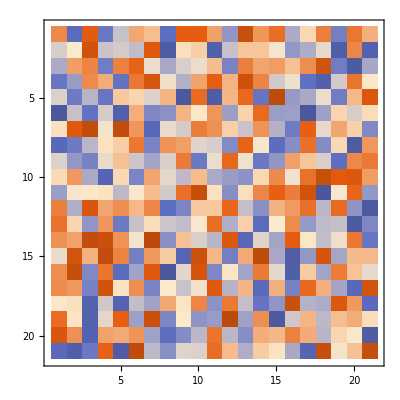

```mathematica
(* visualizaing the coefficent matrix *)
MatrixPlot[A,PlotTheme->"Scientific"]
```

## 7. Solution of linear system using several different methods

### 7a. Solution by Gaussian Elimination and back substitution

```mathematica
(* Define gaussian elimination module *)
GaussianElimination[m_?MatrixQ,v_?VectorQ]:=
Last/@RowReduce[Flatten/@Transpose[{m,-v}]]

(* compute solution *)
solution7a=GaussianElimination[A,B];
```

### 7b. Solution by row reduce of augmented matrix

```mathematica
rra[A_?MatrixQ, B_?VectorQ] := Module[
    {u,r},

   (*build the agumented matrix*)
    u=Transpose[Append[Transpose[A],-B]];
    
    (*row reduce the augmented matrix to find the inverse*)
    r=RowReduce[augmented];

    (*take the last column *)
    r[[All,22]]
];

(* compute solution *)
solution7b = rra[A, B];
```

### 7c. Solution matrix equation A.x=b by inverse matrix

```mathematica
(* solving the matrix equation *)
imx[A_?MatrixQ, B_?VectorQ] := Module[{}, Inverse[A].-B];

(* compute solution *)
solution7c = imx[A, B];
```

### 7d. Solution by using Cramer’s Rule

```mathematica
(*cramers rule module *)
crule[m_,b_]:=Module[
{d=Det[m],a},
Table[
a=m;
a[[All,k]]=-b;
Det[a]/d,
{k,Length[m]}
]
];

solution7d = crule[A,B];
```

## 8. Solution verification and analysis

```mathematica
(* control solution using mathematics built in solve module *)controlSolution=Values/@Solve[system,dimensions][[1]];
```

```mathematica
(* verify that all methods gave the same solution *)allSolutionsMatch = (controlSolution==solution7a==solution7b==solution7c==solution7d)
```

True

```mathematica
(* verify that the solution solves the system *)
(* create a set of rules by mapping dimensions of members of soltuion vector *)
solution=Rule@@@Transpose[{dimensions,solution7a}];
MatrixForm[solution]
```

(x1→0.834403
x2→0.278551
x3→0.750225
x4→-0.877223
x5→-0.67107
x6→1.63143
x7→-0.151417
x8→-0.122025
x9→-0.885059
x10→0.652412
x11→-0.788524
x12→-1.31481
x13→-2.04559
x14→-0.428833
x15→-1.51564
x16→0.452994
x17→0.293732
x18→-0.711651
x19→-0.894227
x20→0.222595
x21→1.37145)

```mathematica
(* substitute the solution values into each equation in the system *)
solutionSolvesEquaion = (system/.solution)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

## 9. Description of eigenvalues

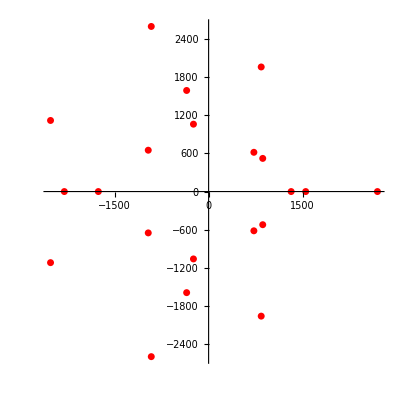

```mathematica
(* compute eigenvalues and eigenvectors *)
{eval,evec}=Eigensystem[A];

(* visualize eigenvalues *)
ComplexListPlot[eval,PlotStyle->Directive[Red,AbsolutePointSize[5]]]
```

## 10. Results

```mathematica
(* variable holding results of test that all solutions are the same*)
allSolutionsMatch
```

True

```mathematica
(* variable indicating if all solutions test as being equal *)
AllTrue[system ,ReplaceAll[solution]]
```

True

```mathematica
(* measure the timing of each method *)
{timingControl, ci} = Timing[Values/@Solve[system,dimensions][[1]]];
{timingA, ai} =Timing[GaussianElimination[A,-B]];
{timingB, bi} = Timing[rra[A, B]];
{timingC, ci} = Timing[imx[A, B]];
{timingD, di} = Timing[crule[A,-B]];
timings = {timingControl, timingA, timingB, timingC, timingD};
```

```mathematica
Print[
"control:", timingControl,
", a: ", timingA,
 ", b: ",timingB,
", c: ", timingC,
", d: ", timingD
]
```

control:0.001139, a: 0.000135, b: 0.000128, c: 0.000069, d: 0.000917

```mathematica
(* vector form of our solution *)
solution = MatrixForm[solution7a]
```

(0.834403
0.278551
0.750225
-0.877223
-0.67107
1.63143
-0.151417
-0.122025
-0.885059
0.652412
-0.788524
-1.31481
-2.04559
-0.428833
-1.51564
0.452994
0.293732
-0.711651
-0.894227
0.222595
1.37145)

## 11. Discussion

We can visualize that our solutions are all equal by plotting them on contour map

```mathematica
labels ={"control", "gaussian", "augmented", "inverse", "cramers"};
```

```mathematica
autolabel[labelfn_]:=labelfn/@Charting`ScaledTicks[{Identity,Identity}][#1,#2]&
framelabel[{x0_,label:Except[_Spacer],{plen_,mlen_},style_}]:={x0,labels[[label]],{plen,mlen},style};
framelabel[tick_]:=tick;
```

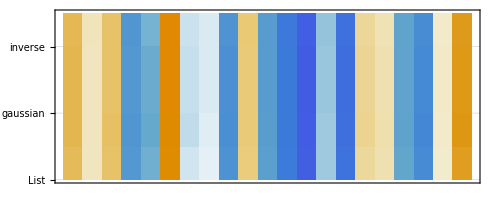

```mathematica
(* visualizing matching solutions *)
MatrixPlot[{controlSolution, solution7a, solution7b, solution7c, solution7d},PlotTheme->"HeightGrid", 
GridLines->{None, Automatic}, 
FrameTicks->{{autolabel[framelabel],None},{None,None}}
]
```

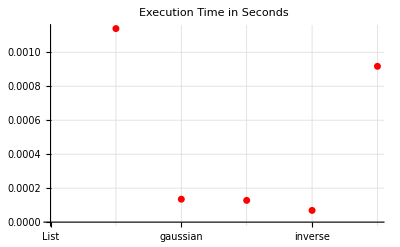

```mathematica
(* visualizing solution execution timing *)
ListPlot[timings, PlotStyle->Directive[Red,AbsolutePointSize[5]],
GridLinesStyle->{Automatic, Directive[Gray, Thin, Dashed]},
GridLines->Automatic,
Ticks->{autolabel[framelabel], Automatic},
PlotLabel-> "Execution Time in Seconds"
]
```

## 12. Full Detailed Answer

With these results we are ready to answer our research questions:

Are all methods equivalently accurate?

The solutions were compared to the 6th decimal place and found to be equal.

Are all methods equivalently precise?

The solutions were compared to the 6th decimal place and found to be equal.

Are all methods equivalently efficient, both to code and execute?

The methods are not equivalently efficient, three of the methods were close in speed while Cramer’s rule was measured to be much slower. Using the inverse matrix to solve the matrix equation was measured to be the fastest at 0.000075s. Applying cramers rule was the slowest method, measuring at  0.000842s. Gaussian with back substitution and row-reducing the augmented matrix both came in in the middle at 0.000129s and 0.000183s. All methods were measured to be faster then the built-in Solve function.

## 13. Conclusions

The 21 dimension linear system was evaluated using implementations of gaussian back substitution, row reduction of augmented matrix, inverse to solve matrix equation, and cramers rule.

All methods were found to be equally accurate and precise to 6 decimal places.

All methods were faster then mathematics built in Solve function, and among them cramers rule showed to be much slower then the other three.

Custom implementations of algorithms should be used when speed is a concern. While our system is still small and the execution of each took under a second, relying on built-ins like Mathematica ‘solve’ function will be more costly as size increases.

## 14. Learning outcomes

Ability to collaborate successfully.

Understand the process of group development

Ability to motivate and empower others

Utilizes others’ contributions effectively

## 15. Individual contribution of each team member

Polina Zhukov (50%)

Richard Larancuente (50%)

## References

Rosen, K, Elementary Number Theory and its applications [book]. Addison Wesley Longman, 2000.

Linear algebra, Wikipedia.com [online], https://en.wikipedia.org/wiki/Linear_algebra,  2001.

IEEE citation standards, ieee.org [online], http://www.ieee.org/documents/ieeecitationref.pdf, 2018.

Hill cipher. Wikipedia.com [online],
https://en.wikipedia.org/wiki/Hill_cipher, 2004.

Cramer’s Rule [online], rosettacode.comhttps://rosettacode.org/wiki/Cramer%27s_rule